## Prebivalstvo Slovenije Analiza prebivalstva Slovenije glede na različne dejavnike.

## Pridobivanje podatkov

Podatke sem pridobila iz STATISTIČNEGA URADA REPUBLIKE SLOVENIJE.

```mathematica
graf =Import["C:\\Users\\uporabnik\\Desktop\\Projekt-ROM\\prebivalstvoSlo.xlsx","Dataset","HeaderLines"-> 1 ][[1]]
```

## Analiza podatkov o prebivalstvu Slovenije glede na spol

Analizirala in narisala bom graf števila prebivalcev Slovenije glede na spol - za Državljane Republike Slovenije in še za Tuje državljane.  Z grafom je lepo prikazano, katerega spola je več in katerega manj, po letu katerega si izberemo od 2008 - 2021.

```mathematica
LetniPrikazPoKategorijah[leto_]:=PieChart3D[Table[graf[Select[#"Leto"==leto&&#"Četrtletje"==1.0&],{3,4,6,7}][1,i],{i,4}],ImageSize->Large,ChartLegends->{"M - DRS","Ž - DRS","M - tujci","Ž - tujke"}]
```

```mathematica
LetniPrikazPoKategorijah[2015]
```

-Graphics3D-

## Analiza podatkov o prebivalstvu Slovenije glede na čas

Analizirala bom celotno prebivalstvo Slovenije glede na čas, torej po letih. Z grafoma bom prikazala v katerem letu je bilo največ prebivalcev in posledično tudi, kdaj jih je bilo najmanj za državljene RS in tuje državljane.

```mathematica
poLetihDRS = graf[Select[#"Četrtletje" == 1.0&], {8, 2}]
```

### SPOL - SKUPAJ (državljani RS)

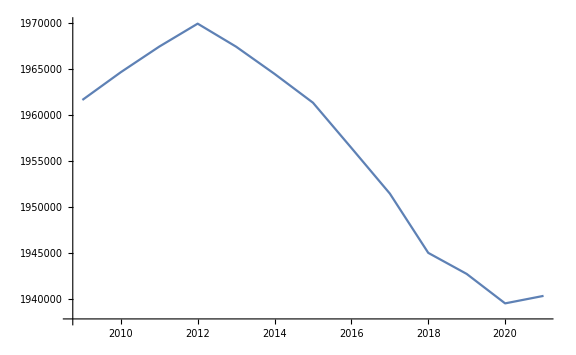

```mathematica
ListLinePlot[poLetihDRS, ImageSize -> Large]
```

### SPOL - SKUPAJ (tuji državljani)

```mathematica
poLetihTujci = graf[Select[#"Četrtletje" == 1.0&], {8, 5}]
```

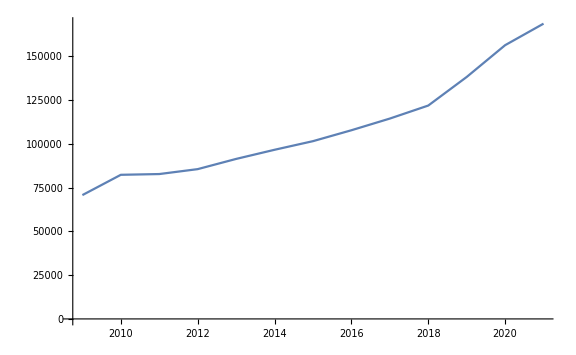

```mathematica
ListLinePlot[poLetihTujci, ImageSize -> Large]
```